(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 29 Kb

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{h→Function[{x},1-Tanh[A x]^2],g→Function[{x},ⅈ Tanh[A x]]}}

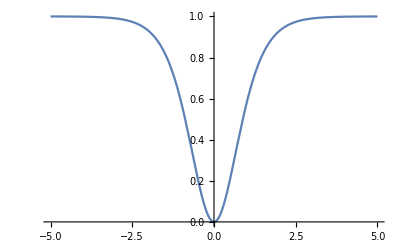

```mathematica
<<Utilities`CleanSlate`;
CleanSlate[];
ClearAll["Global`*"];
s=DSolve[{h'[x]==2*I*A*h[x]*g[x],g'[x]==I*A*h[x],h[0]==1,g[0]==0},{h,g},x]
Plot[With[{A=1},Abs[g[x]]^2/.s],{x,-5,5}]
```